# Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Зарина Азимова Группа: ТФ-11-22 Задача № 3

### -Graphics-

#### Введем исходные данные:

```mathematica
d0=UnitConvert[Quantity[100,"Millimeters"],"Meters"];

r0=d0/2;L=Quantity[0.12,"Meters"];t0=Quantity[800,"DegreesCelsius"];tLiquid=Quantity[25,"DegreesCelsius"];α=Quantity[70,("Watts")/(("Meters")^2*"Kelvins")];
ρ=Quantity[7785,("Kilograms")/("Meters")^3];
cp=Quantity[460,("Joules")/("Kilograms"*"Kelvins")];
λ=Quantity[31,("Watts")/("Meters"*"Kelvins")];
τ1=UnitConvert[Quantity[1.2,"Minutes"],"Seconds"];
```

#### Найдем коэффициент температуропроводности a:

```mathematica
a=UnitConvert[N[λ/(cp*ρ)],("Meters")^2/("Seconds")]
```

8.65656×10^-6 m^2/s

#### Числа Био по радиальному( BiRadial) и вертикальному( BiVertical) направлениям:

```mathematica
BiRadial=N[(α*r0)/λ]
```

0.112903

```mathematica
BiVertical=N[(α*L/2)/λ]
```

0.135484

#### Числа Фурье по радиальному( FoRadial) и вертикальному( FoVertical) направлениям:

```mathematica
FoRadial=(a*τ1)/(r0)^2
```

0.249309

```mathematica
FoVertical=(a*τ1)/(L/2)^2
```

0.173131

#### Приступим к поиску корней характеристического уравнения(MATLAB) в радиальном направлении.В точках разрыва присваиваем NaN чтобы не цепляло лишних корней, либо без NaN но выкидываем лишние корни после численного расчета.В картинках ниже производилах фильтрация корней. Скрипты прилагаются: -Graphics- Седьмой корень отдельно: -Graphics-

```mathematica
ϵ={0.4686   , 3.8611,    7.0317   ,10.1846,   13.3322   ,16.4775 ,  19.6216};
```

#### В вертикальном направлении: -Graphics- Отдельно седьмой корень: -Graphics-

```mathematica
μ={0.3600    ,3.1841   , 6.3047    ,9.4391  , 12.5771,   15.7166   ,18.8567};
```

#### Найдем функцию распределения температуры в радиальном направлении:

```mathematica
ΘRadial[r_,τ_]:=Total[(2*BesselJ[1,ϵ])/(ϵ*(BesselJ[0,ϵ]+BesselJ[1,ϵ]^2))*BesselJ[0,ϵ*r/QuantityMagnitude[r0]]*Exp[-ϵ^2*QuantityMagnitude[a]*τ/QuantityMagnitude[r0]^2]];
```

```mathematica
ΘRadial[0,0]
```

0.999578

```mathematica
tRadial[r_,τ_]=tLiquid+(t0-tLiquid)*ΘRadial[r,τ];
```

#### Найдем температуру на оси цилиндра в момент времени τ = 0 . (оно тут иногда показывает почему то 298.021К но в расчетах далее это нормальные 1072К, можете сами прокомпилировать << tLiquid+(t0-tLiquid)*ΘRadial[0,0] >>). Видимо просто баг какой-то.

```mathematica
tRadial[0,0]
```

1072.82 K

#### Нормальное tRadial[0,0]

```mathematica
tRadial[0,0]=tLiquid+(t0-tLiquid)*ΘRadial[0,0]
```

1072.82 K

```mathematica
UnitConvert[tRadial[0,0],"DegreesCelsius"]
```

799.673 °C

#### Найдем функцию распределения температуры в вертикальном направлении:

```mathematica
ΘVertical[x_,τ_]:=Total[(2*Sin[μ])/(μ+Sin[μ]*Cos[μ])*Cos[μ*x/QuantityMagnitude[L/2]]*Exp[-μ^2*(QuantityMagnitude[a]*τ)/QuantityMagnitude[(L/2)^2]]]
```

```mathematica
ΘVertical[0,0]
```

1.00033

```mathematica
tVertical[x_,τ_]:=tLiquid + (t0-tLiquid)*ΘVertical[x,τ];
```

#### Найдем температуру в центре цилиндра в момент времени τ = 0

```mathematica
tVertical[0,0]
```

1073.41 K

```mathematica
UnitConvert[tVertical[0,0],"DegreesCelsius"]
```

800.259 °C

#### Найдем функцию распределения температурного поля в цилиндре t(x,r,τ)

```mathematica
Θ3D[x_,r_,τ_]:=ΘVertical[x,τ]*ΘRadial[r,τ];
```

```mathematica
t[x_,r_,τ_]:=tLiquid + (t0-tLiquid)*Θ3D[x,r,τ];
```

#### Начнем расчет температурного поля Сначала для r=0:

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.06 m | 697.248 °C
0.045 m | 716.289 °C
0.03 m | 728.325 °C
0.015 m | 734.637 °C
0. | 736.556 °C)

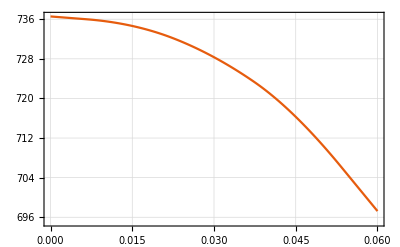

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для r=r0

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.06 m | 660.485 °C
0.045 m | 678.485 °C
0.03 m | 689.863 °C
0.015 m | 695.829 °C
0. | 697.644 °C)

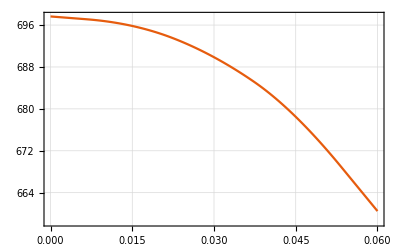

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=0

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.05 m | 697.644 °C
0.0375 m | 714.414 °C
0.025 m | 726.619 °C
0.0125 m | 734.055 °C
0. | 736.556 °C)

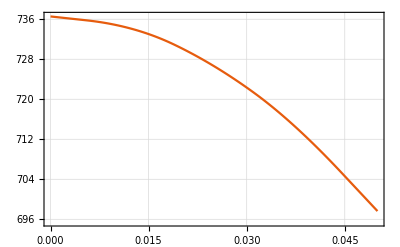

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=L/2

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.05 m | 660.485 °C
0.0375 m | 676.329 °C
0.025 m | 687.86 °C
0.0125 m | 694.886 °C
0. | 697.248 °C)

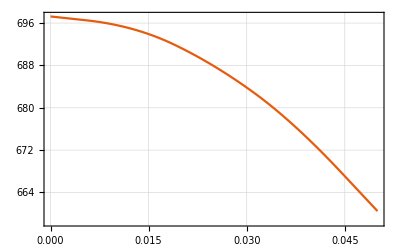

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Покажем распределение температуры в центре цилиндра и на расстоянии 0.2 d_0 от поверхности как функцию времени Сначала для центра:

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[3]}]//MatrixForm
```

(72. s | 736.556 °C
144. s | 685.923 °C
216. s | 637.231 °C)

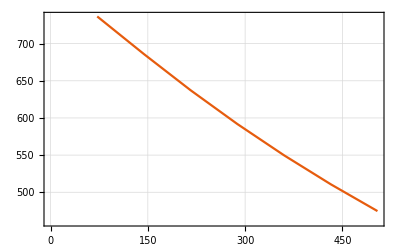

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[7]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь на расстоянии 0.2 d_0 (0.4 r_0)от поверхности , следовательно r=0.6 r_0)

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[7]}]//MatrixForm
```

(72. s | 722.298 °C
144. s | 672.92 °C
216. s | 625.191 °C
288. s | 580.674 °C
360. s | 539.41 °C
432. s | 501.202 °C
504. s | 465.83 °C)

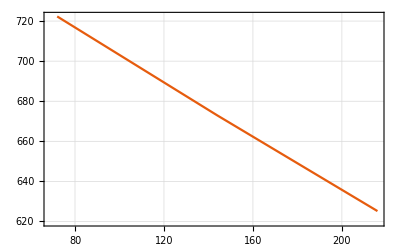

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[3]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Для определения темпа охлаждения и коэффициента температуропроводности заготовки построит несколько зависимостей ln(θ) используя данные полученные выше( в центре и на 0.6r_0). θ = t-tLiquid

```mathematica
lnForCenter=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[7]}]
```

{{72. s,6.56745},{144. s,6.49364},{216. s,6.41711},{288. s,6.34004},{360. s,6.26288},{432. s,6.1857},{504. s,6.10852}}

```mathematica
lnForPoint6r0=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[7]}]
```

{{72. s,6.54721},{144. s,6.47377},{216. s,6.39725},{288. s,6.32018},{360. s,6.24302},{432. s,6.16584},{504. s,6.08866}}

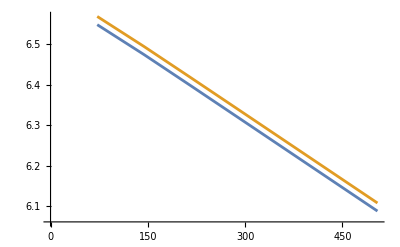

```mathematica
ListLinePlot[{lnForPoint6r0,lnForCenter}]
```

#### Нетрудно заметить,что стадии. регулярного режима гарантированно соответствует интервал [200,500] s. Найдем число Фурье в краевых точках интервала регулярного режима и удостоверимся что оно больше 0.3. Даже если оно не больше 0.3 то мы все равно можем посчитать все,хоть и с погрешностью.

```mathematica
FoRadialAt200=(a*Quantity[200,"Seconds"])/r0^2
```

0.692525

```mathematica
FoRadialAt500=(a*Quantity[500,"Seconds"])/r0^2
```

1.73131

```mathematica
FoVerticalAt200=(a*Quantity[200,"Seconds"])/(L/2)^2
```

0.48092

```mathematica
FoVerticalAt500=(a*Quantity[500,"Seconds"])/(L/2)^2
```

1.2023

#### Приступим к поиску темпа охлаждения m для наших двух точек

```mathematica
mAtCenter=Log[Θ3D[0,0,200]/Θ3D[0,0,500]]/Quantity[500-200,"Seconds"]
```

0.00107128 per second

```mathematica
mAtPoint6r0=Log[Θ3D[0,QuantityMagnitude[0.6*r0],200]/Θ3D[0,QuantityMagnitude[0.6*r0],500]]/Quantity[500-200,"Seconds"]
```

0.00107128 per second

#### Берем среднее

```mathematica
m=(mAtCenter+mAtPoint6r0)/2
```

0.00107128 per second

#### Fo > 0.3 поэтому ряд Фурье сходится быстро и первый член достаточно описывает все решение. Найдем коэффициент формы K:

```mathematica
K=1/((First[ϵ]/r0)^2+(First[μ]/(L/2))^2)
```

0.0080753 m^2

#### Найдем коэффициент температуропроводности по второй теореме Кондратьева(допущение что наше m=m_∞) и сравним с теоретическим:

```mathematica
aExperimental=K*m
```

8.65093×10^-6 m^2/s

```mathematica
a
```

8.65656×10^-6 m^2/s

```mathematica
δa=Abs[a-aExperimental]/a
```

0.000649643

#### Найдем количество теплоты, отданное цилиндром за время τ_1: Для начала найдем сколько теплоты он отдаст до того момента как Θ==1 т.е. t=tLiquid

```mathematica
Q=N[π*(r0)^2*L*ρ*cp*(t0-tLiquid)]
```

2.61571×10^6 J

```mathematica
ΘRadialAverage=Total[(4*BiRadial^2)/(ϵ^2*(ϵ^2+BiRadial^2))*Exp[-ϵ^2*FoRadial]]
```

0.946203

```mathematica
ΘVerticalAverage=Total[(2*Sin[μ]^2)/(μ^2+μ*Sin[μ]*Cos[μ])*Exp[-μ^2*FoVertical]]
```

0.977499

```mathematica
ΘAverage=ΘVerticalAverage*ΘRadialAverage
```

0.924912

```mathematica
Qτ1=Q(1-ΘAverage)
```

196408. J

#### Подытожим полным температурным полем в момент времени τ_1

```mathematica
Show[ListLinePlot3D[Table[t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]],{x,0,L/2,L/4},{r,0,r0,r0/4}]],Boxed->False]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{x,r,t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]]},{x,0,L/2,L/4},{r,0,r0,r0/4}],1];

ListPlot3D[data,Boxed->True,Mesh->None,PlotStyle->Directive[Opacity[0.7],Yellow],AxesLabel->{"x (m)","r (m)","t (°C)"},LabelStyle->Directive[Medium,Black],InterpolationOrder->4]
```

-Graphics3D-